```mathematica
(*Feynman Lectures: Graph of a motion of a mass on a spring 9-4*)
```

```mathematica
Clear["Global`"]
```

```mathematica
ClearAll[x,y,t,r]
```

```mathematica
s=NDSolve[{x''[t]==-x[t],x[0]==1,x'[0]==0},{x[t],x'[t],x''[t]},{t,0,1.6}]
```

{{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],x''[t]→InterpolatingFunction[…][t]}}

```mathematica
tl=Table[t,{t,0,1.6,0.05}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6}

```mathematica
xl=Table[Evaluate[x[t]]/.s[[1]],{t,0,1.6,0.05}]
```

{1.,0.99875,0.995004,0.988771,0.980067,0.968912,0.955336,0.939373,0.921061,0.900447,0.877583,0.852525,0.825336,0.796084,0.764842,0.731689,0.696707,0.659983,0.62161,0.581683,0.540302,0.497571,0.453596,0.408487,0.362358,0.315322,0.267499,0.219007,0.169967,0.120503,0.0707372,0.0207949,-0.0291995}

```mathematica
vxl=Table[Evaluate[x'[t]]/.s[[1]],{t,0,1.6,0.05}]
```

{-1.35525×10^-20,-0.0499792,-0.0998334,-0.149438,-0.198669,-0.247404,-0.29552,-0.342898,-0.389418,-0.434966,-0.479425,-0.522687,-0.564642,-0.605186,-0.644218,-0.681639,-0.717356,-0.75128,-0.783327,-0.813415,-0.841471,-0.867423,-0.891207,-0.912764,-0.932039,-0.948985,-0.963558,-0.975723,-0.98545,-0.992713,-0.997495,-0.999784,-0.999574}

```mathematica
axl=Table[Evaluate[x''[t]]/.s[[1]],{t,0,1.6,0.05}]
```

{-1.,-0.99875,-0.995004,-0.988771,-0.980066,-0.968911,-0.955336,-0.939373,-0.921068,-0.900441,-0.877579,-0.852527,-0.825334,-0.796084,-0.764842,-0.731689,-0.696708,-0.659983,-0.621611,-0.581682,-0.540303,-0.49757,-0.453597,-0.408486,-0.362358,-0.315323,-0.267499,-0.219006,-0.169967,-0.120503,-0.0707374,-0.0207948,0.0291995}

```mathematica
NumberForm[TableForm[Transpose[{tl,xl,vxl,axl}],TableHeadings->{{},{"t","x","v_x","a_x"}}],3]
```

| t | x | v_x | a_x
 | 0. | 1. | -1.36×10^-20 | -1.
 | 0.05 | 0.999 | -0.05 | -0.999
 | 0.1 | 0.995 | -0.0998 | -0.995
 | 0.15 | 0.989 | -0.149 | -0.989
 | 0.2 | 0.98 | -0.199 | -0.98
 | 0.25 | 0.969 | -0.247 | -0.969
 | 0.3 | 0.955 | -0.296 | -0.955
 | 0.35 | 0.939 | -0.343 | -0.939
 | 0.4 | 0.921 | -0.389 | -0.921
 | 0.45 | 0.9 | -0.435 | -0.9
 | 0.5 | 0.878 | -0.479 | -0.878
 | 0.55 | 0.853 | -0.523 | -0.853
 | 0.6 | 0.825 | -0.565 | -0.825
 | 0.65 | 0.796 | -0.605 | -0.796
 | 0.7 | 0.765 | -0.644 | -0.765
 | 0.75 | 0.732 | -0.682 | -0.732
 | 0.8 | 0.697 | -0.717 | -0.697
 | 0.85 | 0.66 | -0.751 | -0.66
 | 0.9 | 0.622 | -0.783 | -0.622
 | 0.95 | 0.582 | -0.813 | -0.582
 | 1. | 0.54 | -0.841 | -0.54
 | 1.05 | 0.498 | -0.867 | -0.498
 | 1.1 | 0.454 | -0.891 | -0.454
 | 1.15 | 0.408 | -0.913 | -0.408
 | 1.2 | 0.362 | -0.932 | -0.362
 | 1.25 | 0.315 | -0.949 | -0.315
 | 1.3 | 0.267 | -0.964 | -0.267
 | 1.35 | 0.219 | -0.976 | -0.219
 | 1.4 | 0.17 | -0.985 | -0.17
 | 1.45 | 0.121 | -0.993 | -0.121
 | 1.5 | 0.0707 | -0.997 | -0.0707
 | 1.55 | 0.0208 | -1. | -0.0208
 | 1.6 | -0.0292 | -1. | 0.0292

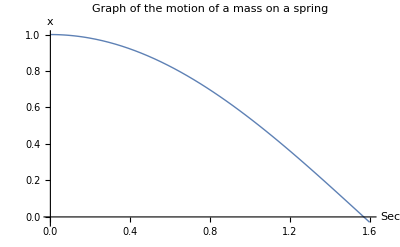

```mathematica
Plot[Evaluate[x[t]]/.s[[1]],{t,0,1.6},PlotRange->All,AxesLabel->{"Sec","x"},AxesStyle->Black,PlotStyle->Thick,PlotLabel->"Graph of the motion of a mass on a spring"]
```

```mathematica
(*Feynman Lectures: Planetary Motions 9-7 in case of GM=1*)
```

```mathematica
ClearAll[x,y,t,r]
```

```mathematica
sol=NDSolve[{x''[t]==(-x[t])/r[t]^3,y''[t]==(-y[t])/r[t]^3,r[t]==√(x[t]^2+y[t]^2),x[0]==0.5,y[0]==0,x'[0]==0,y'[0]==1.639},{x[t],y[t],x'[t],y'[t],x''[t],y''[t],r[t]},{t,0,2.4}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t],x''[t]→InterpolatingFunction[…][t],y''[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

```mathematica
tlist=Table[t,{t,0,2.4,0.05}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4}

```mathematica
xlist=Table[Evaluate[x[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{0.5,0.495017,0.480266,0.456314,0.424027,0.384466,0.338789,0.288162,0.233691,0.176385,0.117136,0.0567144,-0.00422765,-0.0651429,-0.125577,-0.185157,-0.243577,-0.300586,-0.355983,-0.409602,-0.461313,-0.511006,-0.558599,-0.604022,-0.647221,-0.688155,-0.726788,-0.763097,-0.79706,-0.828663,-0.857894,-0.884747,-0.909214,-0.931293,-0.950981,-0.968277,-0.98318,-0.99569,-1.00581,-1.01353,-1.01886,-1.02181,-1.02235,-1.02051,-1.01628,-1.00965,-1.00064,-0.989226,-0.975423}

```mathematica
vxlist=Table[Evaluate[x'[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{5.42101×10^-20,-0.198657,-0.389477,-0.565672,-0.722247,-0.856294,-0.966859,-1.05453,-1.12094,-1.16831,-1.19907,-1.21563,-1.22023,-1.21487,-1.20127,-1.18092,-1.15504,-1.12467,-1.09065,-1.05369,-1.01436,-0.973118,-0.930357,-0.886383,-0.841451,-0.795766,-0.749494,-0.702771,-0.655703,-0.608378,-0.560864,-0.513216,-0.465476,-0.417676,-0.36984,-0.321986,-0.274127,-0.226269,-0.178417,-0.130573,-0.0827363,-0.0349046,0.0129248,0.060755,0.108589,0.15643,0.204278,0.252133,0.299993}

```mathematica
axlist=Table[Evaluate[x''[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{-4.,-3.91978,-3.69011,-3.34091,-2.9124,-2.44642,-1.97832,-1.53415,-1.12986,-0.773086,-0.465382,-0.204533,0.013871,0.194944,0.344023,0.466089,0.565597,0.646423,0.711865,0.764665,0.807127,0.841149,0.868283,0.889809,0.906784,0.920064,0.930355,0.938237,0.944186,0.948591,0.951776,0.954005,0.955494,0.956424,0.956941,0.957165,0.957193,0.957104,0.956959,0.956805,0.956678,0.956601,0.956585,0.956634,0.956742,0.956885,0.957042,0.957161,0.957198}

```mathematica
ylist=Table[Evaluate[y[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{0.,0.0816779,0.16175,0.238733,0.311372,0.378688,0.440004,0.494916,0.543256,0.585041,0.620423,0.649647,0.673018,0.69087,0.703554,0.711419,0.714805,0.71404,0.709435,0.701282,0.689854,0.675408,0.65818,0.638394,0.616255,0.591957,0.565679,0.53759,0.507848,0.476601,0.443989,0.410146,0.375196,0.339261,0.302453,0.264885,0.226662,0.187886,0.14866,0.109079,0.0692408,0.02924,-0.0108292,-0.0508731,-0.0907978,-0.130509,-0.16991,-0.208905,-0.247395}

```mathematica
vylist=Table[Evaluate[y'[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{1.639,1.62272,1.57517,1.49997,1.4023,1.2881,1.1632,1.03274,0.900937,0.770981,0.64513,0.524869,0.411079,0.304193,0.204329,0.111393,0.0251533,-0.0547018,-0.128527,-0.196692,-0.259567,-0.317507,-0.370852,-0.419916,-0.46499,-0.506341,-0.544212,-0.578823,-0.610372,-0.639038,-0.66498,-0.68834,-0.709245,-0.727804,-0.744116,-0.758265,-0.770323,-0.780351,-0.788399,-0.794506,-0.798704,-0.801013,-0.801444,-0.799999,-0.796671,-0.791444,-0.784292,-0.77518,-0.764062}

```mathematica
aylist=Table[Evaluate[y''[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{4.33681×10^-19,-0.646756,-1.24281,-1.74789,-2.13867,-2.40965,-2.56935,-2.63489,-2.62657,-2.5642,-2.46496,-2.34256,-2.20762,-2.06748,-1.92741,-1.79082,-1.65982,-1.53558,-1.41865,-1.30918,-1.20699,-1.11176,-1.02307,-0.940448,-0.863403,-0.791451,-0.724124,-0.660977,-0.601591,-0.545579,-0.492578,-0.442253,-0.394295,-0.348416,-0.304349,-0.261845,-0.220671,-0.180605,-0.14144,-0.102974,-0.0650145,-0.027366,0.0101404,0.0476892,0.0854785,0.123689,0.162507,0.202135,0.242772}

```mathematica
rlist=Table[Evaluate[r[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{0.5,0.50171,0.506772,0.514991,0.526071,0.539647,0.555321,0.572694,0.591387,0.611052,0.631384,0.652118,0.673031,0.693935,0.714673,0.735119,0.755166,0.77473,0.79374,0.81214,0.829885,0.846938,0.863269,0.878857,0.893681,0.907728,0.920985,0.933445,0.9451,0.955945,0.965976,0.97519,0.983587,0.991163,0.99792,1.00385,1.00897,1.01326,1.01673,1.01938,1.02121,1.02222,1.02241,1.02178,1.02033,1.01805,1.01496,1.01104,1.00631}

```mathematica
NumberForm[TableForm[Transpose[{tlist,xlist,vxlist,axlist,ylist,vylist,aylist,rlist,1/rlist^3}],TableHeadings->{{},{"t","x","v_x","a_x","y","v_y","a_y","r","1/r^3"}}],4]
```

| t | x | v_x | a_x | y | v_y | a_y | r | 1/r^3
 | 0. | 0.5 | 5.421×10^-20 | -4. | 0. | 1.639 | 4.337×10^-19 | 0.5 | 8.
 | 0.05 | 0.495 | -0.1987 | -3.92 | 0.08168 | 1.623 | -0.6468 | 0.5017 | 7.918
 | 0.1 | 0.4803 | -0.3895 | -3.69 | 0.1617 | 1.575 | -1.243 | 0.5068 | 7.684
 | 0.15 | 0.4563 | -0.5657 | -3.341 | 0.2387 | 1.5 | -1.748 | 0.515 | 7.322
 | 0.2 | 0.424 | -0.7222 | -2.912 | 0.3114 | 1.402 | -2.139 | 0.5261 | 6.869
 | 0.25 | 0.3845 | -0.8563 | -2.446 | 0.3787 | 1.288 | -2.41 | 0.5396 | 6.363
 | 0.3 | 0.3388 | -0.9669 | -1.978 | 0.44 | 1.163 | -2.569 | 0.5553 | 5.839
 | 0.35 | 0.2882 | -1.055 | -1.534 | 0.4949 | 1.033 | -2.635 | 0.5727 | 5.324
 | 0.4 | 0.2337 | -1.121 | -1.13 | 0.5433 | 0.9009 | -2.627 | 0.5914 | 4.835
 | 0.45 | 0.1764 | -1.168 | -0.7731 | 0.585 | 0.771 | -2.564 | 0.6111 | 4.383
 | 0.5 | 0.1171 | -1.199 | -0.4654 | 0.6204 | 0.6451 | -2.465 | 0.6314 | 3.973
 | 0.55 | 0.05671 | -1.216 | -0.2045 | 0.6496 | 0.5249 | -2.343 | 0.6521 | 3.606
 | 0.6 | -0.004228 | -1.22 | 0.01387 | 0.673 | 0.4111 | -2.208 | 0.673 | 3.28
 | 0.65 | -0.06514 | -1.215 | 0.1949 | 0.6909 | 0.3042 | -2.067 | 0.6939 | 2.993
 | 0.7 | -0.1256 | -1.201 | 0.344 | 0.7036 | 0.2043 | -1.927 | 0.7147 | 2.74
 | 0.75 | -0.1852 | -1.181 | 0.4661 | 0.7114 | 0.1114 | -1.791 | 0.7351 | 2.517
 | 0.8 | -0.2436 | -1.155 | 0.5656 | 0.7148 | 0.02515 | -1.66 | 0.7552 | 2.322
 | 0.85 | -0.3006 | -1.125 | 0.6464 | 0.714 | -0.0547 | -1.536 | 0.7747 | 2.151
 | 0.9 | -0.356 | -1.091 | 0.7119 | 0.7094 | -0.1285 | -1.419 | 0.7937 | 2.
 | 0.95 | -0.4096 | -1.054 | 0.7647 | 0.7013 | -0.1967 | -1.309 | 0.8121 | 1.867
 | 1. | -0.4613 | -1.014 | 0.8071 | 0.6899 | -0.2596 | -1.207 | 0.8299 | 1.75
 | 1.05 | -0.511 | -0.9731 | 0.8411 | 0.6754 | -0.3175 | -1.112 | 0.8469 | 1.646
 | 1.1 | -0.5586 | -0.9304 | 0.8683 | 0.6582 | -0.3709 | -1.023 | 0.8633 | 1.554
 | 1.15 | -0.604 | -0.8864 | 0.8898 | 0.6384 | -0.4199 | -0.9404 | 0.8789 | 1.473
 | 1.2 | -0.6472 | -0.8415 | 0.9068 | 0.6163 | -0.465 | -0.8634 | 0.8937 | 1.401
 | 1.25 | -0.6882 | -0.7958 | 0.9201 | 0.592 | -0.5063 | -0.7915 | 0.9077 | 1.337
 | 1.3 | -0.7268 | -0.7495 | 0.9304 | 0.5657 | -0.5442 | -0.7241 | 0.921 | 1.28
 | 1.35 | -0.7631 | -0.7028 | 0.9382 | 0.5376 | -0.5788 | -0.661 | 0.9334 | 1.23
 | 1.4 | -0.7971 | -0.6557 | 0.9442 | 0.5078 | -0.6104 | -0.6016 | 0.9451 | 1.185
 | 1.45 | -0.8287 | -0.6084 | 0.9486 | 0.4766 | -0.639 | -0.5456 | 0.9559 | 1.145
 | 1.5 | -0.8579 | -0.5609 | 0.9518 | 0.444 | -0.665 | -0.4926 | 0.966 | 1.109
 | 1.55 | -0.8847 | -0.5132 | 0.954 | 0.4101 | -0.6883 | -0.4423 | 0.9752 | 1.078
 | 1.6 | -0.9092 | -0.4655 | 0.9555 | 0.3752 | -0.7092 | -0.3943 | 0.9836 | 1.051
 | 1.65 | -0.9313 | -0.4177 | 0.9564 | 0.3393 | -0.7278 | -0.3484 | 0.9912 | 1.027
 | 1.7 | -0.951 | -0.3698 | 0.9569 | 0.3025 | -0.7441 | -0.3043 | 0.9979 | 1.006
 | 1.75 | -0.9683 | -0.322 | 0.9572 | 0.2649 | -0.7583 | -0.2618 | 1.004 | 0.9885
 | 1.8 | -0.9832 | -0.2741 | 0.9572 | 0.2267 | -0.7703 | -0.2207 | 1.009 | 0.9736
 | 1.85 | -0.9957 | -0.2263 | 0.9571 | 0.1879 | -0.7804 | -0.1806 | 1.013 | 0.9612
 | 1.9 | -1.006 | -0.1784 | 0.957 | 0.1487 | -0.7884 | -0.1414 | 1.017 | 0.9514
 | 1.95 | -1.014 | -0.1306 | 0.9568 | 0.1091 | -0.7945 | -0.103 | 1.019 | 0.944
 | 2. | -1.019 | -0.08274 | 0.9567 | 0.06924 | -0.7987 | -0.06501 | 1.021 | 0.939
 | 2.05 | -1.022 | -0.0349 | 0.9566 | 0.02924 | -0.801 | -0.02737 | 1.022 | 0.9362
 | 2.1 | -1.022 | 0.01292 | 0.9566 | -0.01083 | -0.8014 | 0.01014 | 1.022 | 0.9357
 | 2.15 | -1.021 | 0.06076 | 0.9566 | -0.05087 | -0.8 | 0.04769 | 1.022 | 0.9374
 | 2.2 | -1.016 | 0.1086 | 0.9567 | -0.0908 | -0.7967 | 0.08548 | 1.02 | 0.9414
 | 2.25 | -1.01 | 0.1564 | 0.9569 | -0.1305 | -0.7914 | 0.1237 | 1.018 | 0.9477
 | 2.3 | -1.001 | 0.2043 | 0.957 | -0.1699 | -0.7843 | 0.1625 | 1.015 | 0.9564
 | 2.35 | -0.9892 | 0.2521 | 0.9572 | -0.2089 | -0.7752 | 0.2021 | 1.011 | 0.9676
 | 2.4 | -0.9754 | 0.3 | 0.9572 | -0.2474 | -0.7641 | 0.2428 | 1.006 | 0.9813

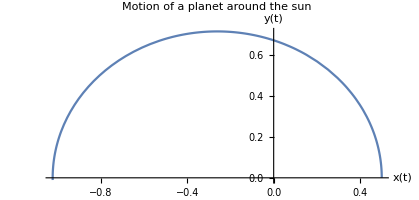

```mathematica
ClickPane[ParametricPlot[Evaluate[{x[t],y[t]}]/.sol[[1]],{t,0,2.1},AxesLabel->{"x(t)","y(t)"},PlotLabel->"Motion of a planet around the sun"],(xycoord=#)&]
```

```mathematica
Dynamic[xycoord]
```

```mathematica
(*Planetary Motion: in case of GM=4 π^2-> Reference:H.Gould,J.Tobochnik,and W.Christian.An Introduction to Computer Simulation
Methods:Applications to Physical Systems,Third Edition.Addison-Wesley,San Francisco,2007.Page: 108 *)
```

```mathematica
ClearAll[x,y,t,r]
```

```mathematica
sol=NDSolve[{x''[t]==(-(4 π^2)x[t])/r[t]^3,y''[t]==(-(4 π^2)y[t])/r[t]^3,r[t]==√(x[t]^2+y[t]^2),x[0]==1,y[0]==0,x'[0]==π,y'[0]==2π},{x[t],y[t],x'[t],y'[t],x''[t],y''[t],r[t]},{t,0,2.4}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t],x''[t]→InterpolatingFunction[…][t],y''[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

```mathematica
tlist=Table[t,{t,0,2.4,0.05}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4}

```mathematica
xlist=Table[Evaluate[x[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{1.,1.11263,1.15331,1.14175,1.09155,1.01225,0.91074,0.792164,0.66052,0.519024,0.370361,0.21686,0.060625,-0.0963613,-0.25215,-0.40474,-0.551986,-0.691489,-0.820462,-0.935536,-1.03249,-1.10584,-1.14819,-1.14923,-1.09415,-0.961582,-0.72317,-0.35668,0.102429,0.532133,0.842035,1.03058,1.12625,1.15468,1.13412,1.07719,0.992777,0.887336,0.765743,0.631806,0.488612,0.33876,0.184523,0.0279711,-0.128927,-0.284219,-0.435881,-0.581724,-0.719282}

```mathematica
vxlist=Table[Evaluate[x'[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{3.14159,1.45507,0.237151,-0.654993,-1.32153,-1.82768,-2.21584,-2.51403,-2.7411,-2.90985,-3.02896,-3.1041,-3.1387,-3.13428,-3.09064,-3.00585,-2.87602,-2.69487,-2.4529,-2.13614,-1.72398,-1.18567,-0.474503,0.481536,1.79232,3.60765,6.02055,8.54595,9.35076,7.51838,4.9016,2.74428,1.16847,0.0287103,-0.809618,-1.43834,-1.91703,-2.28453,-2.56661,-2.78066,-2.93848,-3.04806,-3.11456,-3.14098,-3.12847,-3.07649,-2.98272,-2.84283,-2.64994}

```mathematica
axlist=Table[Evaluate[x''[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{-39.4784,-28.5068,-20.6956,-15.3199,-11.5545,-8.83003,-6.78795,-5.20141,-3.92341,-2.85527,-1.92772,-1.08943,-0.299585,0.477187,1.27483,2.12959,3.08415,4.19318,5.53143,7.20659,9.38046,12.3045,16.3778,22.2267,30.722,42.3436,53.011,41.1829,-13.4875,-51.4913,-49.2567,-36.9472,-26.635,-19.4074,-14.4271,-10.9165,-8.35815,-6.42625,-4.91401,-3.6866,-2.65262,-1.7475,-0.922374,-0.138074,0.640223,1.44662,2.3183,3.29996,4.44965}

```mathematica
ylist=Table[Evaluate[y[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{0.,0.310026,0.601214,0.865833,1.10156,1.3082,1.48633,1.63676,1.76031,1.85771,1.92956,1.97627,1.99816,1.99535,1.96782,1.91541,1.83779,1.73448,1.60487,1.44821,1.26365,1.05042,0.808041,0.537042,0.240575,-0.0715223,-0.372793,-0.601462,-0.66141,-0.516644,-0.245701,0.0652996,0.372526,0.658568,0.91727,1.14693,1.34758,1.51987,1.66465,1.7827,1.87475,1.94133,1.98287,1.99961,1.99166,1.95898,1.90136,1.81844,1.70972}

```mathematica
vylist=Table[Evaluate[y'[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{6.28319,6.05261,5.57159,5.00643,4.42255,3.84509,3.28274,2.73722,2.20735,1.6907,1.18438,0.685349,0.190546,-0.303081,-0.798579,-1.299,-1.80741,-2.32683,-2.86008,-3.40939,-3.97551,-4.55557,-5.13832,-5.69232,-6.1366,-6.26588,-5.5848,-3.2049,0.961577,4.50801,6.03165,6.27061,5.96533,5.45787,4.88532,4.30147,3.72676,3.1679,2.62579,2.0989,1.58464,1.08009,0.582189,0.0878818,-0.405883,-0.902152,-1.40398,-1.91444,-2.43651}

```mathematica
aylist=Table[Evaluate[y''[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{-5.20417×10^-18,-7.94326,-10.7879,-11.6184,-11.6605,-11.4116,-11.078,-10.7471,-10.4561,-10.2197,-10.0433,-9.92814,-9.87415,-9.88109,-9.949,-10.0781,-10.2684,-10.5179,-10.8198,-11.1558,-11.4806,-11.6878,-11.5258,-10.3865,-6.75493,3.14974,27.3273,69.4436,87.0921,49.9924,14.3727,-2.34097,-8.80995,-11.069,-11.6685,-11.6232,-11.3452,-11.0072,-10.6826,-10.4021,-10.178,-10.0143,-9.91187,-9.87056,-9.89017,-9.97079,-10.1127,-10.3155,-10.5767}

```mathematica
rlist=Table[Evaluate[r[t]/.sol[[1]]],{t,0,2.4,0.05}]
```

{1.,1.15501,1.30061,1.43292,1.55078,1.6541,1.74316,1.81838,1.88016,1.92886,1.96478,1.98814,1.99908,1.99767,1.98391,1.9577,1.91889,1.86724,1.80244,1.7241,1.63183,1.52521,1.40402,1.26852,1.12029,0.964239,0.813603,0.699269,0.669295,0.741678,0.87715,1.03265,1.18626,1.32928,1.45864,1.57346,1.67379,1.75994,1.83232,1.89135,1.93737,1.97067,1.99143,1.9998,1.99583,1.97949,1.95068,1.90922,1.85486}

```mathematica
NumberForm[TableForm[Transpose[{tlist,xlist,vxlist,axlist,ylist,vylist,aylist,rlist,1/rlist^3}],TableHeadings->{{},{"t","x","v_x","a_x","y","v_y","a_y","r","1/r^3"}}],4]
```

| t | x | v_x | a_x | y | v_y | a_y | r | 1/r^3
 | 0. | 1. | 3.142 | -39.48 | 0. | 6.283 | -5.204×10^-18 | 1. | 1.
 | 0.05 | 1.113 | 1.455 | -28.51 | 0.31 | 6.053 | -7.943 | 1.155 | 0.649
 | 0.1 | 1.153 | 0.2372 | -20.7 | 0.6012 | 5.572 | -10.79 | 1.301 | 0.4545
 | 0.15 | 1.142 | -0.655 | -15.32 | 0.8658 | 5.006 | -11.62 | 1.433 | 0.3399
 | 0.2 | 1.092 | -1.322 | -11.55 | 1.102 | 4.423 | -11.66 | 1.551 | 0.2681
 | 0.25 | 1.012 | -1.828 | -8.83 | 1.308 | 3.845 | -11.41 | 1.654 | 0.221
 | 0.3 | 0.9107 | -2.216 | -6.788 | 1.486 | 3.283 | -11.08 | 1.743 | 0.1888
 | 0.35 | 0.7922 | -2.514 | -5.201 | 1.637 | 2.737 | -10.75 | 1.818 | 0.1663
 | 0.4 | 0.6605 | -2.741 | -3.923 | 1.76 | 2.207 | -10.46 | 1.88 | 0.1505
 | 0.45 | 0.519 | -2.91 | -2.855 | 1.858 | 1.691 | -10.22 | 1.929 | 0.1393
 | 0.5 | 0.3704 | -3.029 | -1.928 | 1.93 | 1.184 | -10.04 | 1.965 | 0.1318
 | 0.55 | 0.2169 | -3.104 | -1.089 | 1.976 | 0.6853 | -9.928 | 1.988 | 0.1273
 | 0.6 | 0.06063 | -3.139 | -0.2996 | 1.998 | 0.1905 | -9.874 | 1.999 | 0.1252
 | 0.65 | -0.09636 | -3.134 | 0.4772 | 1.995 | -0.3031 | -9.881 | 1.998 | 0.1254
 | 0.7 | -0.2522 | -3.091 | 1.275 | 1.968 | -0.7986 | -9.949 | 1.984 | 0.1281
 | 0.75 | -0.4047 | -3.006 | 2.13 | 1.915 | -1.299 | -10.08 | 1.958 | 0.1333
 | 0.8 | -0.552 | -2.876 | 3.084 | 1.838 | -1.807 | -10.27 | 1.919 | 0.1415
 | 0.85 | -0.6915 | -2.695 | 4.193 | 1.734 | -2.327 | -10.52 | 1.867 | 0.1536
 | 0.9 | -0.8205 | -2.453 | 5.531 | 1.605 | -2.86 | -10.82 | 1.802 | 0.1708
 | 0.95 | -0.9355 | -2.136 | 7.207 | 1.448 | -3.409 | -11.16 | 1.724 | 0.1951
 | 1. | -1.032 | -1.724 | 9.38 | 1.264 | -3.976 | -11.48 | 1.632 | 0.2301
 | 1.05 | -1.106 | -1.186 | 12.3 | 1.05 | -4.556 | -11.69 | 1.525 | 0.2818
 | 1.1 | -1.148 | -0.4745 | 16.38 | 0.808 | -5.138 | -11.53 | 1.404 | 0.3613
 | 1.15 | -1.149 | 0.4815 | 22.23 | 0.537 | -5.692 | -10.39 | 1.269 | 0.4899
 | 1.2 | -1.094 | 1.792 | 30.72 | 0.2406 | -6.137 | -6.755 | 1.12 | 0.7112
 | 1.25 | -0.9616 | 3.608 | 42.34 | -0.07152 | -6.266 | 3.15 | 0.9642 | 1.115
 | 1.3 | -0.7232 | 6.021 | 53.01 | -0.3728 | -5.585 | 27.33 | 0.8136 | 1.857
 | 1.35 | -0.3567 | 8.546 | 41.18 | -0.6015 | -3.205 | 69.44 | 0.6993 | 2.925
 | 1.4 | 0.1024 | 9.351 | -13.49 | -0.6614 | 0.9616 | 87.09 | 0.6693 | 3.335
 | 1.45 | 0.5321 | 7.518 | -51.49 | -0.5166 | 4.508 | 49.99 | 0.7417 | 2.451
 | 1.5 | 0.842 | 4.902 | -49.26 | -0.2457 | 6.032 | 14.37 | 0.8771 | 1.482
 | 1.55 | 1.031 | 2.744 | -36.95 | 0.0653 | 6.271 | -2.341 | 1.033 | 0.9081
 | 1.6 | 1.126 | 1.168 | -26.63 | 0.3725 | 5.965 | -8.81 | 1.186 | 0.599
 | 1.65 | 1.155 | 0.02871 | -19.41 | 0.6586 | 5.458 | -11.07 | 1.329 | 0.4257
 | 1.7 | 1.134 | -0.8096 | -14.43 | 0.9173 | 4.885 | -11.67 | 1.459 | 0.3222
 | 1.75 | 1.077 | -1.438 | -10.92 | 1.147 | 4.301 | -11.62 | 1.573 | 0.2567
 | 1.8 | 0.9928 | -1.917 | -8.358 | 1.348 | 3.727 | -11.35 | 1.674 | 0.2133
 | 1.85 | 0.8873 | -2.285 | -6.426 | 1.52 | 3.168 | -11.01 | 1.76 | 0.1834
 | 1.9 | 0.7657 | -2.567 | -4.914 | 1.665 | 2.626 | -10.68 | 1.832 | 0.1626
 | 1.95 | 0.6318 | -2.781 | -3.687 | 1.783 | 2.099 | -10.4 | 1.891 | 0.1478
 | 2. | 0.4886 | -2.938 | -2.653 | 1.875 | 1.585 | -10.18 | 1.937 | 0.1375
 | 2.05 | 0.3388 | -3.048 | -1.748 | 1.941 | 1.08 | -10.01 | 1.971 | 0.1307
 | 2.1 | 0.1845 | -3.115 | -0.9224 | 1.983 | 0.5822 | -9.912 | 1.991 | 0.1266
 | 2.15 | 0.02797 | -3.141 | -0.1381 | 2. | 0.08788 | -9.871 | 2. | 0.125
 | 2.2 | -0.1289 | -3.128 | 0.6402 | 1.992 | -0.4059 | -9.89 | 1.996 | 0.1258
 | 2.25 | -0.2842 | -3.076 | 1.447 | 1.959 | -0.9022 | -9.971 | 1.979 | 0.1289
 | 2.3 | -0.4359 | -2.983 | 2.318 | 1.901 | -1.404 | -10.11 | 1.951 | 0.1347
 | 2.35 | -0.5817 | -2.843 | 3.3 | 1.818 | -1.914 | -10.32 | 1.909 | 0.1437
 | 2.4 | -0.7193 | -2.65 | 4.45 | 1.71 | -2.437 | -10.58 | 1.855 | 0.1567

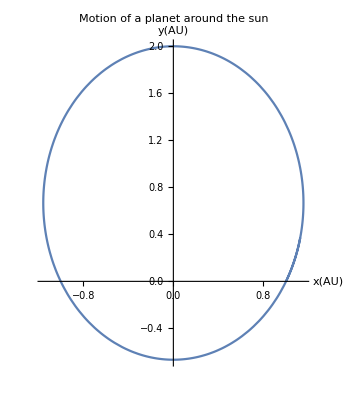

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}]/.sol[[1]],{t,0,1.6},AxesLabel->{"x(AU)","y(AU)"},PlotLabel->"Motion of a planet around the sun"]
```